```mathematica
λ=500*^-9;
k=(2 π)/λ;
w=1*^-3;
z=0.3;
min=-0.01;max=0.01;step=200;
d=(max-min)/step
x=Range[min,max,d];
y=Table[ If[Abs[x]<=w/2,1,0],{x,Range[min,max,d]}];
scale1=λ/(step d);
endx=x scale1;
```

0.0001

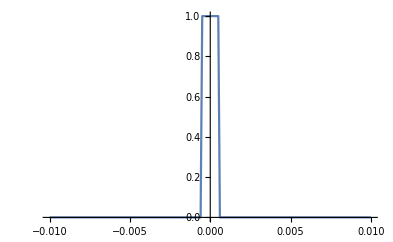

```mathematica
ListLinePlot[y,PlotRange->All,DataRange->{min,max}]
```

```mathematica
yscal=Total[y^2 d]/Total[Abs[Fourier[y^2]]*(endx[[2]]-endx[[1]])];
h2=Exp[I k z]/(I λ z) Exp[(I k)/(2 z)endx^2];
F1=Fourier[y*(-1)^Table[i,{i,Length[x]}]];
FFS1=h2*F1;
```

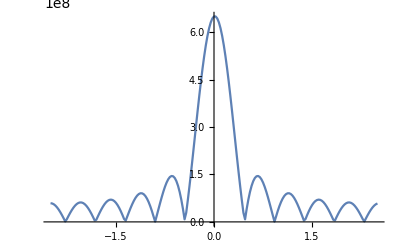

```mathematica
ListLinePlot[Transpose[{endx,Abs[FFS1*√yscal]}],PlotRange->All]
```

```mathematica
ListLinePlot[Transpose[{endx,Abs[FFS1^2*yscal]}],PlotRange->All]
```

-Graphics-

```mathematica
posendx=z*Tan[endx];
```

```mathematica
ListLinePlot[Transpose[{posendx,Abs[FFS1^2*yscal]}],PlotRange->All]
```

-Graphics-